```mathematica
ClearAll["Global`*"]
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"out","vortexDecay"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out/vortexDecay

```mathematica
FileNames[]
```

{cumulant_Re100000_size96,cumulant_Re100000_size96_time,cumulant_Re10000_size96,cumulant_Re10000_size96_time,cumulant_Re2000_size96,cumulant_Re2000_size96_time,cumulant_Re5000_size96,cumulant_Re5000_size96_time,cumulant_Re7000_size96,cumulant_Re7000_size96_time,srt_Re100000_size96,srt_Re10000_size96,srt_Re2000_size96,srt_Re5000_size96,srt_Re7000_size96}

```mathematica
srts = Complement[FileNames[], FileNames["*time"], FileNames["cumulant*"]];
cumulants = Complement[FileNames[], FileNames["*time"], FileNames["srt*"]];
getReynolds[thelist_]:=Read[StringToStream[#],Number]&/@ Flatten[ StringDrop[#,2] &/@StringCases[thelist, RegularExpression["Re([0-9]*)"]]]

srts = srts[[Ordering[getReynolds[srts]]]];
cumulants = cumulants[[Ordering[getReynolds[cumulants]]]];
```

```mathematica
srtsInput = Import /@srts;
cumulantsInput = Import /@cumulants;
```

{srt_Re2000_size96,srt_Re5000_size96,srt_Re7000_size96,srt_Re10000_size96,srt_Re100000_size96}

{cumulant_Re2000_size96,cumulant_Re5000_size96,cumulant_Re7000_size96,cumulant_Re10000_size96,cumulant_Re100000_size96}

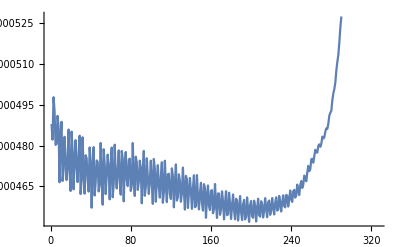

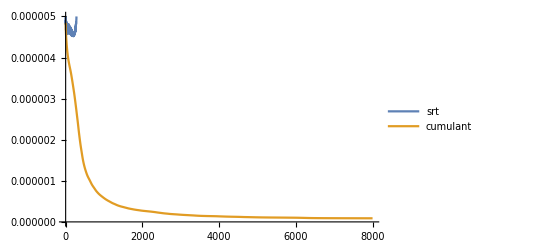

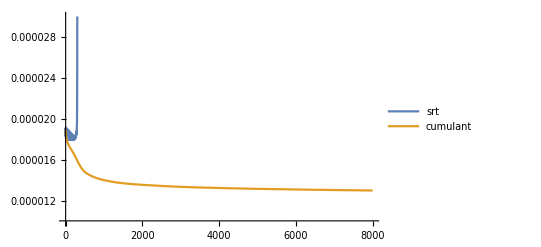

```mathematica
input = 2;

srts
cumulants

enstrophySRT = Flatten[ Take[#,1]&/@srtsInput[[input]]];
tkeSRT = Flatten[Drop[#,1]&/@srtsInput[[input]]];

enstrophyCumulant = Flatten[ Take[#,1]&/@cumulantsInput[[input]]];
tkeCumulant = Flatten[Drop[#,1]&/@cumulantsInput[[input]]];
ListLinePlot[enstrophySRT]
ListLinePlot[{enstrophySRT,enstrophyCumulant}, PlotLegends->Placed[{"srt","cumulant"},{Right,Top}], PlotRange->{0,5*10^-6}]
ListLinePlot[{tkeSRT,tkeCumulant}, PlotLegends->Placed[{"srt","cumulant"},{Right,Top}], PlotRange->{0.00001,0.00003}]
```

{srt_Re2000_size96,srt_Re5000_size96,srt_Re7000_size96,srt_Re10000_size96,srt_Re100000_size96}

{cumulant_Re2000_size96,cumulant_Re5000_size96,cumulant_Re7000_size96,cumulant_Re10000_size96,cumulant_Re100000_size96}

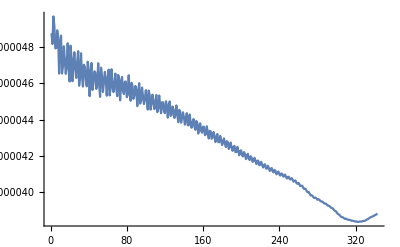

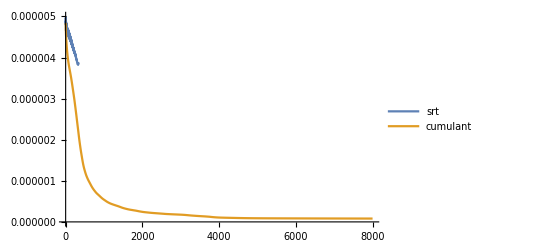

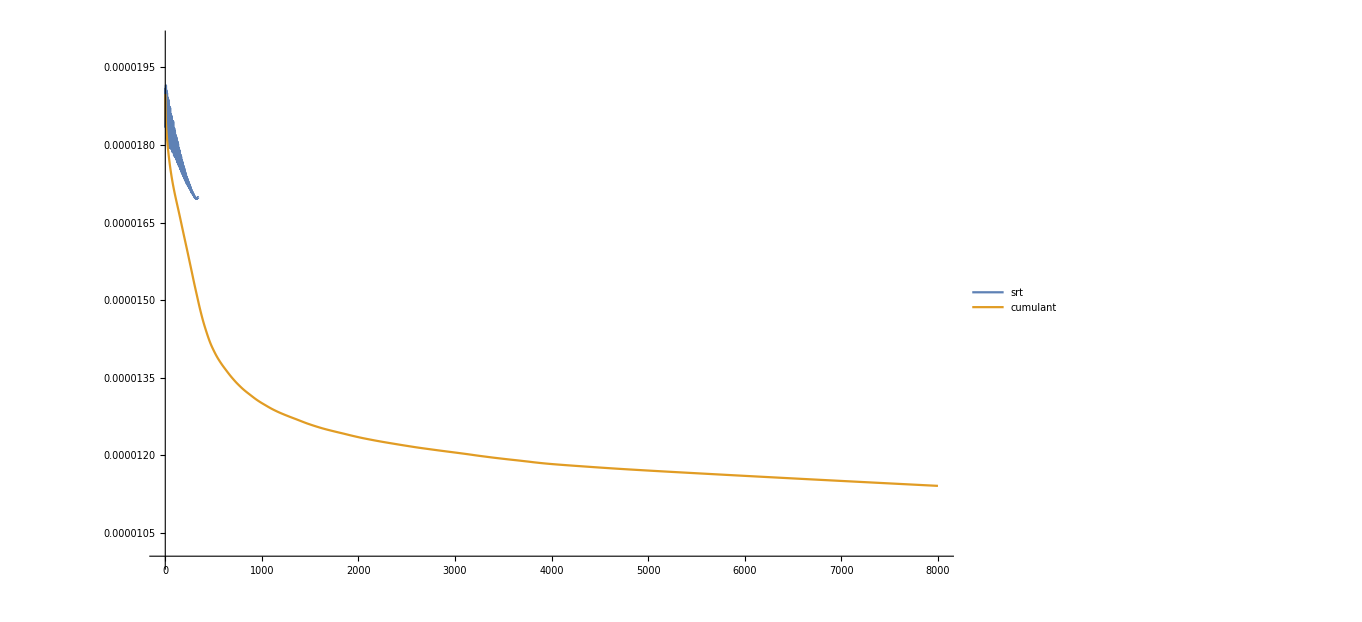

```mathematica
input = 1;

srts
cumulants

enstrophySRT = Flatten[ Take[#,1]&/@srtsInput[[input]]];
tkeSRT = Flatten[Drop[#,1]&/@srtsInput[[input]]];

enstrophyCumulant = Flatten[ Take[#,1]&/@cumulantsInput[[input]]];
tkeCumulant = Flatten[Drop[#,1]&/@cumulantsInput[[input]]];
ListLinePlot[enstrophySRT]
ListLinePlot[{enstrophySRT,enstrophyCumulant}, PlotLegends->Placed[{"srt","cumulant"},{Right,Top}], PlotRange->{0,5*10^-6}]
ListLinePlot[{tkeSRT,tkeCumulant}, PlotLegends->Placed[{"srt","cumulant"},{Right,Top}], PlotRange->{0.00001,0.00002}]
```